```mathematica
up=Import[FileNameJoin[{NotebookDirectory[],"upPoints.dat"}]];
down=Import[FileNameJoin[{NotebookDirectory[],"downPoints.dat"}]];
```

```mathematica
R=35;
n=4;
```

```mathematica
fitter[x_]=Join[{1},Table[(R^i-x^i)/R^i,{i,2,2*n,2}]];
```

```mathematica
lmup =LinearModelFit[up,fitter[x],x];
lmdown =LinearModelFit[down,fitter[x],x]
```

FittedModel[-2.38995-0.00445193 (1225-x^2)-1.61602×10^-8 (1500625-x^4)+1.89162×10^-11 (1838265625-x^6)-1.35005×10^-14 (2251875390625-x^8)]

```mathematica
lmdown["CovarianceMatrix"]
```

{{2.30156×10^-8,4.02259×10^-8,-6.03696×10^-8},{4.02259×10^-8,2.26883×10^-7,-2.39722×10^-7},{-6.03696×10^-8,-2.39722×10^-7,2.75782×10^-7}}

```mathematica
lmdown["ParameterTable"]
```

General::munfl: Exp[-1481.99] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1218.55] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
1 | -2.38975 | 3.31387×10^-6 | -721135. | 0.
(1225-x^2)/1225 | -5.4553 | 0.0000540266 | -100974. | 0.
(1500625-x^4)/1500625 | -0.0151201 | 0.000563997 | -26.8089 | 1.06239×10^-55
(1838265625-x^6)/1838265625 | 0.0341918 | 0.00235032 | 14.5477 | 2.34745×10^-29
(2251875390625-x^8)/2251875390625 | -0.0932007 | 0.00457063 | -20.3912 | 6.59879×10^-43
(2758547353515625-x^10)/2758547353515625 | 0.105615 | 0.0041543 | 25.423 | 4.08552×10^-53
(3379220508056640625-x^12)/3379220508056640625 | -0.0499141 | 0.00142507 | -35.0258 | 2.57877×10^-69

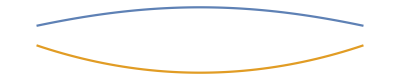

```mathematica
Plot[{lmup[x],lmdown[x]},{x,-35,35},AspectRatio->-1,Axes->False]
```

```mathematica
upR=Import[FileNameJoin[{NotebookDirectory[],"upArcs.dat"}]];
downR=Import[FileNameJoin[{NotebookDirectory[],"downArcs.dat"}]];
```

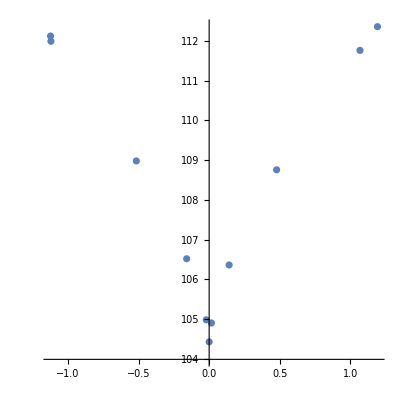

```mathematica
ListPlot[downR[[All,{1,2}]],AspectRatio->1]
```